#### Input

```mathematica
targetSymbol=3x-3x^2-3;
range={-5, 5, 0.1};
```

#### Function and Constants Initialization

```mathematica
toFunc[symb_, var_:x][dontusethisvariable_]:=With[{symb2=symb/.var->dontusethissymbol}, symb2/.{dontusethissymbol->dontusethisvariable}]
funcFromVals[xVals_,vals_][x_]:=Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], {InterpolatingFunction::dmval, InterpolatingFunction::dprec}]
funcFromVals[xVals_,vals_, extrapolatingFunc_][x_]:=If[x<Min[xVals],extrapolatingFunc[x],If[x>Max[xVals],extrapolatingFunc[x],Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], InterpolatingFunction::dprec]]]
```

```mathematica
target=toFunc[targetSymbol];
pRange=AbsoluteOptions[Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
PlotFunc[func_]:=Plot[func[x], {x, range[[1]], range[[2]]}, PlotRange->pRange]
PlotVals[xVals_, vals_, prange_:pRange]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange-> prange], PlotFunc[funcFromVals[xVals, vals]]}]
```

#### Approximation Initialization

```mathematica
(* Find a fixed point of the target, as it gives one point which is definitly on the graph of the functional iterate. *)fixedPoint=x/.Last[NMinimize[{(x-targetSymbol)^2, x∈Interval[range[[1;;2]]]}, x,PrecisionGoal->50]];
fixedPoint=If[Mod[fixedPoint, 1]<=10^-20, Floor[fixedPoint], fixedPoint] (* Rounding, if necesary *)

(* First two terms of Maclaurin series to make a linear approximation around x = fixedPoint *)
twoMaclaurinTerms={targetSymbol/.x->fixedPoint, D[targetSymbol, x]/.x->fixedPoint};

(* y = term[[1]]+term[[2]](x - fixedPoint) -> y = (term[[1]] - term[[2]]fixedPoint) + term[[2]]x *)
twoMaclaurinTerms={twoMaclaurinTerms[[1]] - twoMaclaurinTerms[[2]]*fixedPoint, twoMaclaurinTerms[[2]]};

(* Half-Iterate of Maxlaurin Terms (can be complex sometimes) *)
approxSymbol=N[twoMaclaurinTerms[[1]]/(1+√twoMaclaurinTerms[[2]])+√twoMaclaurinTerms[[2]] x] 
originalApproxFunc=toFunc[approxSymbol];
approxFunc=originalApproxFunc;
nestedApproxFunc:=approxFunc[approxFunc[#]]&;
```

0.332156

-1.33216+1.00353 x

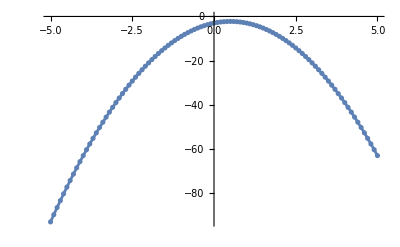

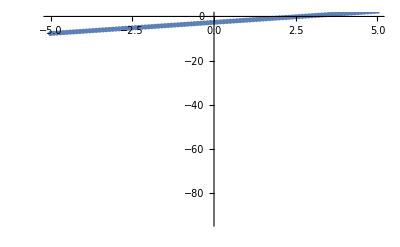

```mathematica
PlotVals[(Range@@range), target/@(Range@@range)]
PlotVals[(Range@@range), nestedApproxFunc/@(Range@@range)]
```

#### Base Values

```mathematica
xVals={fixedPoint}
plots={};

updatenxVals[]:=nxVals=Union[xVals, Clip[#, range[[1;;2]]]&/@{Min[xVals]-range[[3]],Max[xVals]+range[[3]]}];
updatenxVals[]

approxVals=approxFunc/@nxVals;
nestedApproxVals=nestedApproxFunc/@nxVals;
```

{0.332156}

{0.232156,0.332156,0.432156}

#### Running Through Manually

```mathematica
approxVals
```

{-0.1,0,0.1}

```mathematica
deltaVals=(target/@nxVals)-nestedApproxVals
e=Plus@@(deltaVals^2)
newApproxVals=(approxVals+0.5*deltaVals)
approxFunc=funcFromVals[nxVals, newApproxVals,originalApproxFunc]
```

{-0.687415,-0.274917,0.115072}

{-1.93004,-0.274917,1.28989}

{0.0251572,2.83729×10^-9,0.0251572}

0.00126577

{0.0251572,0.,0.0251572}

{-0.674837,-0.274917,0.127651}

funcFromVals[{-0.374917,-0.274917,-0.174917},{-0.674837,-0.274917,0.127651},toFunc[0.828171+4.01244 x]]

{-0.374917,-0.274917,-0.174917}

{-0.474917,-0.374917,-0.274917,-0.174917,-0.0749172}

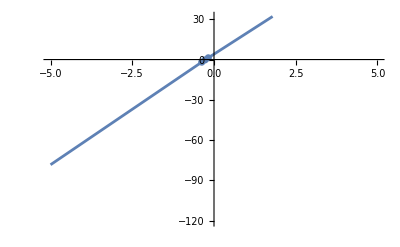

```mathematica
plots=AppendTo[plots, PlotVals[nxVals, nestedApproxVals]];
xVals=nxVals
updatenxVals[]
plots
```

```mathematica
FixedPoint[updateApproxVals, 0., 100]
plots=AppendTo[plots, PlotVals[nxVals, nestedApproxVals]];
xVals=nxVals
updatenxVals[]
plots
```

$Aborted

$Aborted

{-0.474917,-0.374917,-0.274917,-0.174917,-0.0749172}

{-0.574917,-0.474917,-0.374917,-0.274917,-0.174917,-0.0749172,0.0250828}

{-Graphics-}

#### Running Through Automatically

```mathematica
updateApproxVals[nothing_]:=Module[{},
approxVals=approxFunc/@nxVals;
nestedApproxVals=nestedApproxFunc/@nxVals;
deltaVals=(target/@nxVals)-nestedApproxVals;
e=Plus@@(deltaVals^2);
deltaVals=deltaVals*Table[If[i==1||i==Length[deltaVals], 1, 0], {i, Length[deltaVals]}];
newApproxVals=(approxVals+0.5*deltaVals);
approxFunc=funcFromVals[nxVals, newApproxVals];
e]
```

```mathematica
updateApproxValsOPTIMIZED[nothing_]:=Module[{},
approxVals=approxFunc/@nxVals;
nestedApproxVals=nestedApproxFunc/@nxVals;
deltaVals=(target/@{First[nxVals], Last[nxVals]})-{First[nestedApproxVals],Last[nestedApproxVals]};
e=Plus@@(deltaVals^2);
newApproxVals=approxVals;
newApproxVals[[1]]=newApproxVals[[1]]+0.5*deltaVals[[1]];
newApproxVals[[Length[newApproxVals]]]=newApproxVals[[Length[newApproxVals]]]+0.5*deltaVals[[2]];
approxFunc=funcFromVals[nxVals, newApproxVals];
e]
```

RUN THIS:

```mathematica
While[xVals!=nxVals,
p1=FixedPoint[updateApproxValsOPTIMIZED, 0., 100];
AppendTo[plots, PlotVals[nxVals, nestedApproxVals, Automatic]];

xVals=nxVals;
p2=SymmetricDifference[updatenxVals[], xVals];

NotebookDelete[progress];
progress=PrintTemporary[{p1,p2,Last[plots]}];
];
```

#### Output

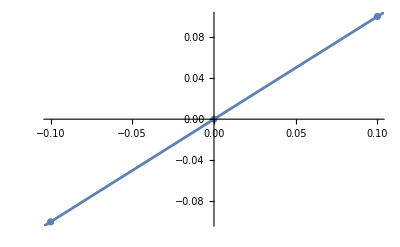
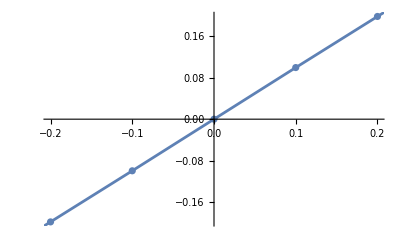
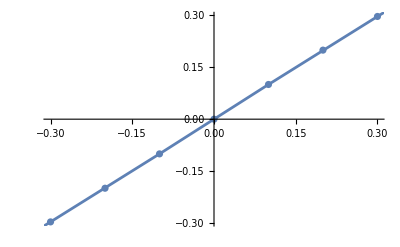
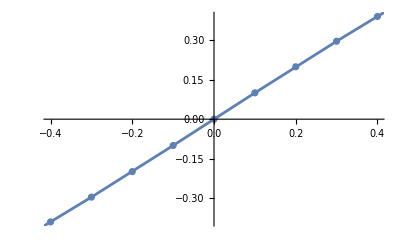
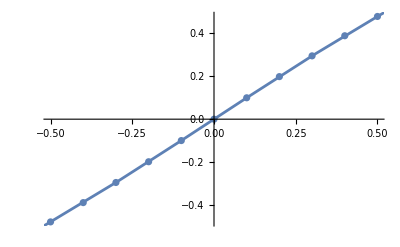
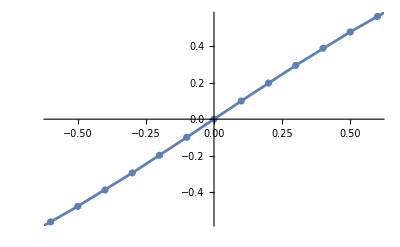
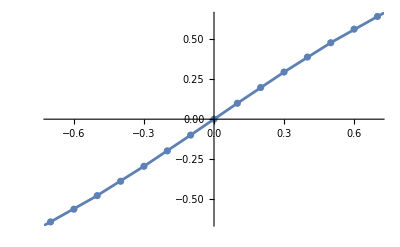
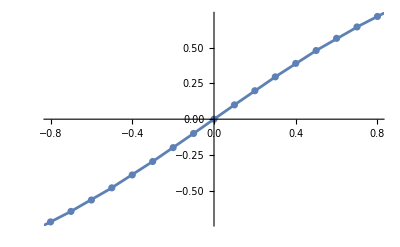

```mathematica
plots
```

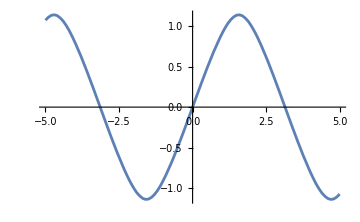
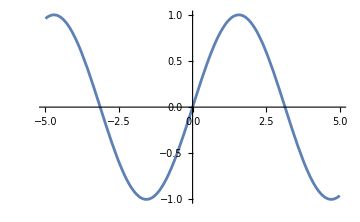
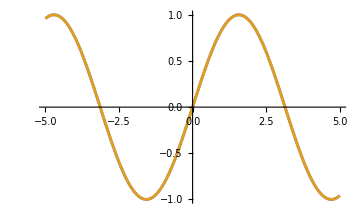
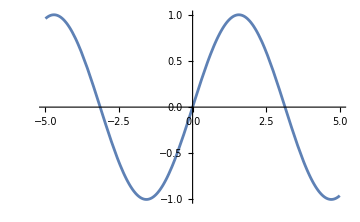
-Graphics-approx | -Graphics-approx nested
-Graphics-both | -Graphics-target

```mathematica
pSize=Medium;

pTarget=Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->pSize];
pApprox=Plot[approxFunc[x], {x, range[[1]], range[[2]]}, ImageSize->pSize];
pApproxNested=Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->pSize, PlotRange->pRange];
pBoth=Plot[{target[x],approxFunc[approxFunc[x]]}, {x, range[[1]], range[[2]]}, ImageSize->pSize];

Grid[{{Labeled[pApprox, "approx"], Labeled[pApproxNested, "approx nested"]},
{Labeled[pBoth, "both"], Labeled[pTarget, "target"]}}]
```